```mathematica
K:=10^(-10)*E^(6.86*10^3/T)
```

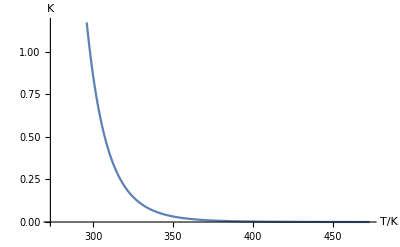

```mathematica
Plot[K,{T,273.15,(273.15+200)},AxesLabel->{"T/K","K"}]
```

```mathematica
E0:=5.7*10^(-9)/(E^(-6.86*10^3/T)+10^(-10))
```

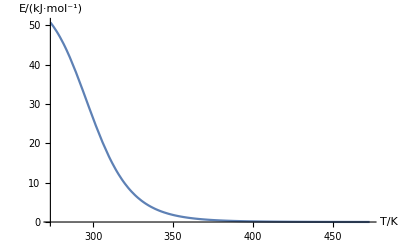

```mathematica
Plot[E0,{T,273.15,(273.15+200)},AxesLabel->{"T/K","E/(kJ·mol^-1)"}]
```

```mathematica
K1:=0.1*E^(6.86*10^2/T)
```

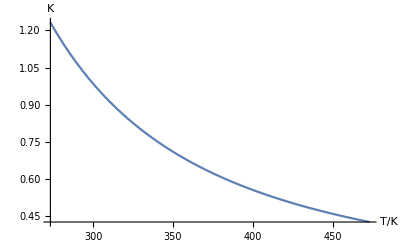

```mathematica
Plot[K1,{T,273.15,(273.15+200)},AxesLabel->{"T/K","K"}]
```

```mathematica
E01:=5.7/(E^(-6.86*10^2/T)+0.1)
```

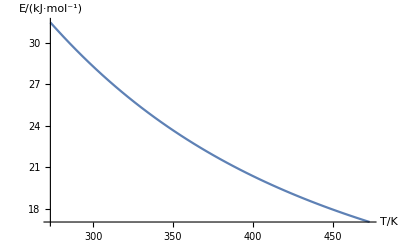

```mathematica
Plot[E01,{T,273.15,(273.15+200)},AxesLabel->{"T/K","E/(kJ·mol^-1)"}]
```

```mathematica
Limit[5.7*10^(-9)/(E^(-6.86*10^3/T)+10^(-10)),T->Infinity]-Limit[5.7*10^(-9)/(E^(-6.86*10^3/T)+10^(-10)),T->0,Direction->"FromAbove"]
```

-57.

```mathematica
Limit[5.7/(E^(-6.86*10^2/T)+0.1),T->Infinity]-Limit[5.7/(E^(-6.86*10^2/T)+0.1),T->0,Direction->"FromAbove"]
```

-51.8182